```mathematica
TableForm[
Table[
allGraphs4[k,"colofourrealnull"]->Length[ListofVars[ allGraphs4[k,"colofour"]]]
,{k,allGraphs4NullAtomKeys}
]
]
```

n1x2x3x4→15
n12x3x4→5
n123x4→2
n1234→1
n124x3→2
n12x34→2
n13x2x4→5
n134x2→2
n13x24→2
n14x2x3→5
n14x23→2
n1x23x4→5
n1x234→2
n1x24x3→5
n1x2x34→5

```mathematica
TableForm[
Sort[
Table[
allGraphs6[k,"colofourrealnull"]->Length[ListofVars[ allGraphs6[k,"colofour"]]]
,{k,allGraphs6NullAtomKeys}
],
#1[[2]]>#2[[2]]&
]
]
```

n1x2x3x4x5x6→203
n1x2x3x4x56→52
n1x2x3x46x5→52
n1x2x3x45x6→52
n1x2x36x4x5→52
n1x2x35x4x6→52
n1x2x34x5x6→52
n1x26x3x4x5→52
n1x25x3x4x6→52
n1x24x3x5x6→52
n1x23x4x5x6→52
n16x2x3x4x5→52
n15x2x3x4x6→52
n14x2x3x5x6→52
n13x2x4x5x6→52
n12x3x4x5x6→52
n1x2x3x456→15
n1x2x36x45→15
n1x2x35x46→15
n1x2x356x4→15
n1x2x34x56→15
n1x2x346x5→15
n1x2x345x6→15
n1x26x3x45→15
n1x26x35x4→15
n1x26x34x5→15
n1x25x3x46→15
n1x25x36x4→15
n1x25x34x6→15
n1x256x3x4→15
n1x24x3x56→15
n1x24x36x5→15
n1x24x35x6→15
n1x246x3x5→15
n1x245x3x6→15
n1x23x4x56→15
n1x23x46x5→15
n1x23x45x6→15
n1x236x4x5→15
n1x235x4x6→15
n1x234x5x6→15
n16x2x3x45→15
n16x2x35x4→15
n16x2x34x5→15
n16x25x3x4→15
n16x24x3x5→15
n16x23x4x5→15
n15x2x3x46→15
n15x2x36x4→15
n15x2x34x6→15
n15x26x3x4→15
n15x24x3x6→15
n15x23x4x6→15
n156x2x3x4→15
n14x2x3x56→15
n14x2x36x5→15
n14x2x35x6→15
n14x26x3x5→15
n14x25x3x6→15
n14x23x5x6→15
n146x2x3x5→15
n145x2x3x6→15
n13x2x4x56→15
n13x2x46x5→15
n13x2x45x6→15
n13x26x4x5→15
n13x25x4x6→15
n13x24x5x6→15
n136x2x4x5→15
n135x2x4x6→15
n134x2x5x6→15
n12x3x4x56→15
n12x3x46x5→15
n12x3x45x6→15
n12x36x4x5→15
n12x35x4x6→15
n12x34x5x6→15
n126x3x4x5→15
n125x3x4x6→15
n124x3x5x6→15
n123x4x5x6→15
n1x2x3456→5
n1x26x345→5
n1x25x346→5
n1x256x34→5
n1x24x356→5
n1x246x35→5
n1x245x36→5
n1x2456x3→5
n1x23x456→5
n1x236x45→5
n1x235x46→5
n1x2356x4→5
n1x234x56→5
n1x2346x5→5
n1x2345x6→5
n16x2x345→5
n16x25x34→5
n16x24x35→5
n16x245x3→5
n16x23x45→5
n16x235x4→5
n16x234x5→5
n15x2x346→5
n15x26x34→5
n15x24x36→5
n15x246x3→5
n15x23x46→5
n15x236x4→5
n15x234x6→5
n156x2x34→5
n156x24x3→5
n156x23x4→5
n14x2x356→5
n14x26x35→5
n14x25x36→5
n14x256x3→5
n14x23x56→5
n14x236x5→5
n14x235x6→5
n146x2x35→5
n146x25x3→5
n146x23x5→5
n145x2x36→5
n145x26x3→5
n145x23x6→5
n1456x2x3→5
n13x2x456→5
n13x26x45→5
n13x25x46→5
n13x256x4→5
n13x24x56→5
n13x246x5→5
n13x245x6→5
n136x2x45→5
n136x25x4→5
n136x24x5→5
n135x2x46→5
n135x26x4→5
n135x24x6→5
n1356x2x4→5
n134x2x56→5
n134x26x5→5
n134x25x6→5
n1346x2x5→5
n1345x2x6→5
n12x3x456→5
n12x36x45→5
n12x35x46→5
n12x356x4→5
n12x34x56→5
n12x346x5→5
n12x345x6→5
n126x3x45→5
n126x35x4→5
n126x34x5→5
n125x3x46→5
n125x36x4→5
n125x34x6→5
n1256x3x4→5
n124x3x56→5
n124x36x5→5
n124x35x6→5
n1246x3x5→5
n1245x3x6→5
n123x4x56→5
n123x46x5→5
n123x45x6→5
n1236x4x5→5
n1235x4x6→5
n1234x5x6→5
n1x23456→2
n16x2345→2
n15x2346→2
n156x234→2
n14x2356→2
n146x235→2
n145x236→2
n1456x23→2
n13x2456→2
n136x245→2
n135x246→2
n1356x24→2
n134x256→2
n1346x25→2
n1345x26→2
n13456x2→2
n12x3456→2
n126x345→2
n125x346→2
n1256x34→2
n124x356→2
n1246x35→2
n1245x36→2
n12456x3→2
n123x456→2
n1236x45→2
n1235x46→2
n12356x4→2
n1234x56→2
n12346x5→2
n12345x6→2
n123456→1

```mathematica
Table[
Length[ListofVars[ allGraphs6[k,"colofour"]]]
,{k,allGraphs6NullAtomKeys}
]//Tally//Sort
```

{{1,1},{2,31},{5,90},{15,65},{52,15},{203,1}}

```mathematica
allGraphs6AtomKeys=Select[Keys[allGraphs6],Length[ListofVars[allGraphs6[#,"colofour"]]]==1&];Length[allGraphs6AtomKeys]
```

203

```mathematica
Table[
Length[ListofVars[ allGraphs6[k,"colofourrealnull"]]]
,{k,allGraphs6AtomKeys}
]//Tally//Sort
```

{{1,1},{2,31},{5,90},{15,65},{52,15},{203,1}}

```mathematica
Table[
allGraphs6[k,"colofourrealnull"]
,{k,allGraphs6AtomKeys}
]//Sort//TableForm
```

n123456
-n123456+n12345x6
-n123456+n12346x5
-n123456+n1234x56
2 n123456-n12345x6-n12346x5-n1234x56+n1234x5x6
-n123456+n12356x4
-n123456+n1235x46
2 n123456-n12345x6-n12356x4-n1235x46+n1235x4x6
-n123456+n1236x45
2 n123456-n12346x5-n12356x4-n1236x45+n1236x4x5
-n123456+n123x456
2 n123456-n12345x6-n1236x45-n123x456+n123x45x6
2 n123456-n12346x5-n1235x46-n123x456+n123x46x5
2 n123456-n1234x56-n12356x4-n123x456+n123x4x56
-6 n123456+2 n12345x6+2 n12346x5+n1234x56-n1234x5x6+2 n12356x4+n1235x46-n1235x4x6+n1236x45-n1236x4x5+2 n123x456-n123x45x6-n123x46x5-n123x4x56+n123x4x5x6
-n123456+n12456x3
-n123456+n1245x36
2 n123456-n12345x6-n12456x3-n1245x36+n1245x3x6
-n123456+n1246x35
2 n123456-n12346x5-n12456x3-n1246x35+n1246x3x5
-n123456+n124x356
2 n123456-n12345x6-n1246x35-n124x356+n124x35x6
2 n123456-n12346x5-n1245x36-n124x356+n124x36x5
2 n123456-n1234x56-n12456x3-n124x356+n124x3x56
-6 n123456+2 n12345x6+2 n12346x5+n1234x56-n1234x5x6+2 n12456x3+n1245x36-n1245x3x6+n1246x35-n1246x3x5+2 n124x356-n124x35x6-n124x36x5-n124x3x56+n124x3x5x6
-n123456+n1256x34
2 n123456-n12356x4-n12456x3-n1256x34+n1256x3x4
-n123456+n125x346
2 n123456-n12345x6-n1256x34-n125x346+n125x34x6
2 n123456-n12356x4-n1245x36-n125x346+n125x36x4
2 n123456-n1235x46-n12456x3-n125x346+n125x3x46
-6 n123456+2 n12345x6+2 n12356x4+n1235x46-n1235x4x6+2 n12456x3+n1245x36-n1245x3x6+n1256x34-n1256x3x4+2 n125x346-n125x34x6-n125x36x4-n125x3x46+n125x3x4x6
-n123456+n126x345
2 n123456-n12346x5-n1256x34-n126x345+n126x34x5
2 n123456-n12356x4-n1246x35-n126x345+n126x35x4
2 n123456-n1236x45-n12456x3-n126x345+n126x3x45
-6 n123456+2 n12346x5+2 n12356x4+n1236x45-n1236x4x5+2 n12456x3+n1246x35-n1246x3x5+n1256x34-n1256x3x4+2 n126x345-n126x34x5-n126x35x4-n126x3x45+n126x3x4x5
-n123456+n12x3456
2 n123456-n12345x6-n126x345-n12x3456+n12x345x6
2 n123456-n12346x5-n125x346-n12x3456+n12x346x5
2 n123456-n1234x56-n1256x34-n12x3456+n12x34x56
-6 n123456+2 n12345x6+2 n12346x5+n1234x56-n1234x5x6+2 n1256x34+n125x346-n125x34x6+n126x345-n126x34x5+2 n12x3456-n12x345x6-n12x346x5-n12x34x56+n12x34x5x6
2 n123456-n12356x4-n124x356-n12x3456+n12x356x4
2 n123456-n1235x46-n1246x35-n12x3456+n12x35x46
-6 n123456+2 n12345x6+2 n12356x4+n1235x46-n1235x4x6+2 n1246x35+n124x356-n124x35x6+n126x345-n126x35x4+2 n12x3456-n12x345x6-n12x356x4-n12x35x46+n12x35x4x6
2 n123456-n1236x45-n1245x36-n12x3456+n12x36x45
-6 n123456+2 n12346x5+2 n12356x4+n1236x45-n1236x4x5+2 n1245x36+n124x356-n124x36x5+n125x346-n125x36x4+2 n12x3456-n12x346x5-n12x356x4-n12x36x45+n12x36x4x5
2 n123456-n123x456-n12456x3-n12x3456+n12x3x456
-6 n123456+2 n12345x6+2 n1236x45+n123x456-n123x45x6+2 n12456x3+n1245x36-n1245x3x6+n126x345-n126x3x45+2 n12x3456-n12x345x6-n12x36x45-n12x3x456+n12x3x45x6
-6 n123456+2 n12346x5+2 n1235x46+n123x456-n123x46x5+2 n12456x3+n1246x35-n1246x3x5+n125x346-n125x3x46+2 n12x3456-n12x346x5-n12x35x46-n12x3x456+n12x3x46x5
-6 n123456+2 n1234x56+2 n12356x4+n123x456-n123x4x56+2 n12456x3+n124x356-n124x3x56+n1256x34-n1256x3x4+2 n12x3456-n12x34x56-n12x356x4-n12x3x456+n12x3x4x56
24 n123456-6 n12345x6-6 n12346x5-2 n1234x56+2 n1234x5x6-6 n12356x4-2 n1235x46+2 n1235x4x6-2 n1236x45+2 n1236x4x5-2 n123x456+n123x45x6+n123x46x5+n123x4x56-n123x4x5x6-6 n12456x3-2 n1245x36+2 n1245x3x6-2 n1246x35+2 n1246x3x5-2 n124x356+n124x35x6+n124x36x5+n124x3x56-n124x3x5x6-2 n1256x34+2 n1256x3x4-2 n125x346+n125x34x6+n125x36x4+n125x3x46-n125x3x4x6-2 n126x345+n126x34x5+n126x35x4+n126x3x45-n126x3x4x5-6 n12x3456+2 n12x345x6+2 n12x346x5+n12x34x56-n12x34x5x6+2 n12x356x4+n12x35x46-n12x35x4x6+n12x36x45-n12x36x4x5+2 n12x3x456-n12x3x45x6-n12x3x46x5-n12x3x4x56+n12x3x4x5x6
-n123456+n13456x2
-n123456+n1345x26
2 n123456-n12345x6-n13456x2-n1345x26+n1345x2x6
-n123456+n1346x25
2 n123456-n12346x5-n13456x2-n1346x25+n1346x2x5
-n123456+n134x256
2 n123456-n12345x6-n1346x25-n134x256+n134x25x6
2 n123456-n12346x5-n1345x26-n134x256+n134x26x5
2 n123456-n1234x56-n13456x2-n134x256+n134x2x56
-6 n123456+2 n12345x6+2 n12346x5+n1234x56-n1234x5x6+2 n13456x2+n1345x26-n1345x2x6+n1346x25-n1346x2x5+2 n134x256-n134x25x6-n134x26x5-n134x2x56+n134x2x5x6
-n123456+n1356x24
2 n123456-n12356x4-n13456x2-n1356x24+n1356x2x4
-n123456+n135x246
2 n123456-n12345x6-n1356x24-n135x246+n135x24x6
2 n123456-n12356x4-n1345x26-n135x246+n135x26x4
2 n123456-n1235x46-n13456x2-n135x246+n135x2x46
-6 n123456+2 n12345x6+2 n12356x4+n1235x46-n1235x4x6+2 n13456x2+n1345x26-n1345x2x6+n1356x24-n1356x2x4+2 n135x246-n135x24x6-n135x26x4-n135x2x46+n135x2x4x6
-n123456+n136x245
2 n123456-n12346x5-n1356x24-n136x245+n136x24x5
2 n123456-n12356x4-n1346x25-n136x245+n136x25x4
2 n123456-n1236x45-n13456x2-n136x245+n136x2x45
-6 n123456+2 n12346x5+2 n12356x4+n1236x45-n1236x4x5+2 n13456x2+n1346x25-n1346x2x5+n1356x24-n1356x2x4+2 n136x245-n136x24x5-n136x25x4-n136x2x45+n136x2x4x5
-n123456+n13x2456
2 n123456-n12345x6-n136x245-n13x2456+n13x245x6
2 n123456-n12346x5-n135x246-n13x2456+n13x246x5
2 n123456-n1234x56-n1356x24-n13x2456+n13x24x56
-6 n123456+2 n12345x6+2 n12346x5+n1234x56-n1234x5x6+2 n1356x24+n135x246-n135x24x6+n136x245-n136x24x5+2 n13x2456-n13x245x6-n13x246x5-n13x24x56+n13x24x5x6
2 n123456-n12356x4-n134x256-n13x2456+n13x256x4
2 n123456-n1235x46-n1346x25-n13x2456+n13x25x46
-6 n123456+2 n12345x6+2 n12356x4+n1235x46-n1235x4x6+2 n1346x25+n134x256-n134x25x6+n136x245-n136x25x4+2 n13x2456-n13x245x6-n13x256x4-n13x25x46+n13x25x4x6
2 n123456-n1236x45-n1345x26-n13x2456+n13x26x45
-6 n123456+2 n12346x5+2 n12356x4+n1236x45-n1236x4x5+2 n1345x26+n134x256-n134x26x5+n135x246-n135x26x4+2 n13x2456-n13x246x5-n13x256x4-n13x26x45+n13x26x4x5
2 n123456-n123x456-n13456x2-n13x2456+n13x2x456
-6 n123456+2 n12345x6+2 n1236x45+n123x456-n123x45x6+2 n13456x2+n1345x26-n1345x2x6+n136x245-n136x2x45+2 n13x2456-n13x245x6-n13x26x45-n13x2x456+n13x2x45x6
-6 n123456+2 n12346x5+2 n1235x46+n123x456-n123x46x5+2 n13456x2+n1346x25-n1346x2x5+n135x246-n135x2x46+2 n13x2456-n13x246x5-n13x25x46-n13x2x456+n13x2x46x5
-6 n123456+2 n1234x56+2 n12356x4+n123x456-n123x4x56+2 n13456x2+n134x256-n134x2x56+n1356x24-n1356x2x4+2 n13x2456-n13x24x56-n13x256x4-n13x2x456+n13x2x4x56
24 n123456-6 n12345x6-6 n12346x5-2 n1234x56+2 n1234x5x6-6 n12356x4-2 n1235x46+2 n1235x4x6-2 n1236x45+2 n1236x4x5-2 n123x456+n123x45x6+n123x46x5+n123x4x56-n123x4x5x6-6 n13456x2-2 n1345x26+2 n1345x2x6-2 n1346x25+2 n1346x2x5-2 n134x256+n134x25x6+n134x26x5+n134x2x56-n134x2x5x6-2 n1356x24+2 n1356x2x4-2 n135x246+n135x24x6+n135x26x4+n135x2x46-n135x2x4x6-2 n136x245+n136x24x5+n136x25x4+n136x2x45-n136x2x4x5-6 n13x2456+2 n13x245x6+2 n13x246x5+n13x24x56-n13x24x5x6+2 n13x256x4+n13x25x46-n13x25x4x6+n13x26x45-n13x26x4x5+2 n13x2x456-n13x2x45x6-n13x2x46x5-n13x2x4x56+n13x2x4x5x6
-n123456+n1456x23
2 n123456-n12456x3-n13456x2-n1456x23+n1456x2x3
-n123456+n145x236
2 n123456-n12345x6-n1456x23-n145x236+n145x23x6
2 n123456-n12456x3-n1345x26-n145x236+n145x26x3
2 n123456-n1245x36-n13456x2-n145x236+n145x2x36
-6 n123456+2 n12345x6+2 n12456x3+n1245x36-n1245x3x6+2 n13456x2+n1345x26-n1345x2x6+n1456x23-n1456x2x3+2 n145x236-n145x23x6-n145x26x3-n145x2x36+n145x2x3x6
-n123456+n146x235
2 n123456-n12346x5-n1456x23-n146x235+n146x23x5
2 n123456-n12456x3-n1346x25-n146x235+n146x25x3
2 n123456-n1246x35-n13456x2-n146x235+n146x2x35
-6 n123456+2 n12346x5+2 n12456x3+n1246x35-n1246x3x5+2 n13456x2+n1346x25-n1346x2x5+n1456x23-n1456x2x3+2 n146x235-n146x23x5-n146x25x3-n146x2x35+n146x2x3x5
-n123456+n14x2356
2 n123456-n12345x6-n146x235-n14x2356+n14x235x6
2 n123456-n12346x5-n145x236-n14x2356+n14x236x5
2 n123456-n1234x56-n1456x23-n14x2356+n14x23x56
-6 n123456+2 n12345x6+2 n12346x5+n1234x56-n1234x5x6+2 n1456x23+n145x236-n145x23x6+n146x235-n146x23x5+2 n14x2356-n14x235x6-n14x236x5-n14x23x56+n14x23x5x6
2 n123456-n12456x3-n134x256-n14x2356+n14x256x3
2 n123456-n1245x36-n1346x25-n14x2356+n14x25x36
-6 n123456+2 n12345x6+2 n12456x3+n1245x36-n1245x3x6+2 n1346x25+n134x256-n134x25x6+n146x235-n146x25x3+2 n14x2356-n14x235x6-n14x256x3-n14x25x36+n14x25x3x6
2 n123456-n1246x35-n1345x26-n14x2356+n14x26x35
-6 n123456+2 n12346x5+2 n12456x3+n1246x35-n1246x3x5+2 n1345x26+n134x256-n134x26x5+n145x236-n145x26x3+2 n14x2356-n14x236x5-n14x256x3-n14x26x35+n14x26x3x5
2 n123456-n124x356-n13456x2-n14x2356+n14x2x356
-6 n123456+2 n12345x6+2 n1246x35+n124x356-n124x35x6+2 n13456x2+n1345x26-n1345x2x6+n146x235-n146x2x35+2 n14x2356-n14x235x6-n14x26x35-n14x2x356+n14x2x35x6
-6 n123456+2 n12346x5+2 n1245x36+n124x356-n124x36x5+2 n13456x2+n1346x25-n1346x2x5+n145x236-n145x2x36+2 n14x2356-n14x236x5-n14x25x36-n14x2x356+n14x2x36x5
-6 n123456+2 n1234x56+2 n12456x3+n124x356-n124x3x56+2 n13456x2+n134x256-n134x2x56+n1456x23-n1456x2x3+2 n14x2356-n14x23x56-n14x256x3-n14x2x356+n14x2x3x56
24 n123456-6 n12345x6-6 n12346x5-2 n1234x56+2 n1234x5x6-6 n12456x3-2 n1245x36+2 n1245x3x6-2 n1246x35+2 n1246x3x5-2 n124x356+n124x35x6+n124x36x5+n124x3x56-n124x3x5x6-6 n13456x2-2 n1345x26+2 n1345x2x6-2 n1346x25+2 n1346x2x5-2 n134x256+n134x25x6+n134x26x5+n134x2x56-n134x2x5x6-2 n1456x23+2 n1456x2x3-2 n145x236+n145x23x6+n145x26x3+n145x2x36-n145x2x3x6-2 n146x235+n146x23x5+n146x25x3+n146x2x35-n146x2x3x5-6 n14x2356+2 n14x235x6+2 n14x236x5+n14x23x56-n14x23x5x6+2 n14x256x3+n14x25x36-n14x25x3x6+n14x26x35-n14x26x3x5+2 n14x2x356-n14x2x35x6-n14x2x36x5-n14x2x3x56+n14x2x3x5x6
-n123456+n156x234
2 n123456-n12356x4-n1456x23-n156x234+n156x23x4
2 n123456-n12456x3-n1356x24-n156x234+n156x24x3
2 n123456-n1256x34-n13456x2-n156x234+n156x2x34
-6 n123456+2 n12356x4+2 n12456x3+n1256x34-n1256x3x4+2 n13456x2+n1356x24-n1356x2x4+n1456x23-n1456x2x3+2 n156x234-n156x23x4-n156x24x3-n156x2x34+n156x2x3x4
-n123456+n15x2346
2 n123456-n12345x6-n156x234-n15x2346+n15x234x6
2 n123456-n12356x4-n145x236-n15x2346+n15x236x4
2 n123456-n1235x46-n1456x23-n15x2346+n15x23x46
-6 n123456+2 n12345x6+2 n12356x4+n1235x46-n1235x4x6+2 n1456x23+n145x236-n145x23x6+n156x234-n156x23x4+2 n15x2346-n15x234x6-n15x236x4-n15x23x46+n15x23x4x6
2 n123456-n12456x3-n135x246-n15x2346+n15x246x3
2 n123456-n1245x36-n1356x24-n15x2346+n15x24x36
-6 n123456+2 n12345x6+2 n12456x3+n1245x36-n1245x3x6+2 n1356x24+n135x246-n135x24x6+n156x234-n156x24x3+2 n15x2346-n15x234x6-n15x246x3-n15x24x36+n15x24x3x6
2 n123456-n1256x34-n1345x26-n15x2346+n15x26x34
-6 n123456+2 n12356x4+2 n12456x3+n1256x34-n1256x3x4+2 n1345x26+n135x246-n135x26x4+n145x236-n145x26x3+2 n15x2346-n15x236x4-n15x246x3-n15x26x34+n15x26x3x4
2 n123456-n125x346-n13456x2-n15x2346+n15x2x346
-6 n123456+2 n12345x6+2 n1256x34+n125x346-n125x34x6+2 n13456x2+n1345x26-n1345x2x6+n156x234-n156x2x34+2 n15x2346-n15x234x6-n15x26x34-n15x2x346+n15x2x34x6
-6 n123456+2 n12356x4+2 n1245x36+n125x346-n125x36x4+2 n13456x2+n1356x24-n1356x2x4+n145x236-n145x2x36+2 n15x2346-n15x236x4-n15x24x36-n15x2x346+n15x2x36x4
-6 n123456+2 n1235x46+2 n12456x3+n125x346-n125x3x46+2 n13456x2+n135x246-n135x2x46+n1456x23-n1456x2x3+2 n15x2346-n15x23x46-n15x246x3-n15x2x346+n15x2x3x46
24 n123456-6 n12345x6-6 n12356x4-2 n1235x46+2 n1235x4x6-6 n12456x3-2 n1245x36+2 n1245x3x6-2 n1256x34+2 n1256x3x4-2 n125x346+n125x34x6+n125x36x4+n125x3x46-n125x3x4x6-6 n13456x2-2 n1345x26+2 n1345x2x6-2 n1356x24+2 n1356x2x4-2 n135x246+n135x24x6+n135x26x4+n135x2x46-n135x2x4x6-2 n1456x23+2 n1456x2x3-2 n145x236+n145x23x6+n145x26x3+n145x2x36-n145x2x3x6-2 n156x234+n156x23x4+n156x24x3+n156x2x34-n156x2x3x4-6 n15x2346+2 n15x234x6+2 n15x236x4+n15x23x46-n15x23x4x6+2 n15x246x3+n15x24x36-n15x24x3x6+n15x26x34-n15x26x3x4+2 n15x2x346-n15x2x34x6-n15x2x36x4-n15x2x3x46+n15x2x3x4x6
-n123456+n16x2345
2 n123456-n12346x5-n156x234-n16x2345+n16x234x5
2 n123456-n12356x4-n146x235-n16x2345+n16x235x4
2 n123456-n1236x45-n1456x23-n16x2345+n16x23x45
-6 n123456+2 n12346x5+2 n12356x4+n1236x45-n1236x4x5+2 n1456x23+n146x235-n146x23x5+n156x234-n156x23x4+2 n16x2345-n16x234x5-n16x235x4-n16x23x45+n16x23x4x5
2 n123456-n12456x3-n136x245-n16x2345+n16x245x3
2 n123456-n1246x35-n1356x24-n16x2345+n16x24x35
-6 n123456+2 n12346x5+2 n12456x3+n1246x35-n1246x3x5+2 n1356x24+n136x245-n136x24x5+n156x234-n156x24x3+2 n16x2345-n16x234x5-n16x245x3-n16x24x35+n16x24x3x5
2 n123456-n1256x34-n1346x25-n16x2345+n16x25x34
-6 n123456+2 n12356x4+2 n12456x3+n1256x34-n1256x3x4+2 n1346x25+n136x245-n136x25x4+n146x235-n146x25x3+2 n16x2345-n16x235x4-n16x245x3-n16x25x34+n16x25x3x4
2 n123456-n126x345-n13456x2-n16x2345+n16x2x345
-6 n123456+2 n12346x5+2 n1256x34+n126x345-n126x34x5+2 n13456x2+n1346x25-n1346x2x5+n156x234-n156x2x34+2 n16x2345-n16x234x5-n16x25x34-n16x2x345+n16x2x34x5
-6 n123456+2 n12356x4+2 n1246x35+n126x345-n126x35x4+2 n13456x2+n1356x24-n1356x2x4+n146x235-n146x2x35+2 n16x2345-n16x235x4-n16x24x35-n16x2x345+n16x2x35x4
-6 n123456+2 n1236x45+2 n12456x3+n126x345-n126x3x45+2 n13456x2+n136x245-n136x2x45+n1456x23-n1456x2x3+2 n16x2345-n16x23x45-n16x245x3-n16x2x345+n16x2x3x45
24 n123456-6 n12346x5-6 n12356x4-2 n1236x45+2 n1236x4x5-6 n12456x3-2 n1246x35+2 n1246x3x5-2 n1256x34+2 n1256x3x4-2 n126x345+n126x34x5+n126x35x4+n126x3x45-n126x3x4x5-6 n13456x2-2 n1346x25+2 n1346x2x5-2 n1356x24+2 n1356x2x4-2 n136x245+n136x24x5+n136x25x4+n136x2x45-n136x2x4x5-2 n1456x23+2 n1456x2x3-2 n146x235+n146x23x5+n146x25x3+n146x2x35-n146x2x3x5-2 n156x234+n156x23x4+n156x24x3+n156x2x34-n156x2x3x4-6 n16x2345+2 n16x234x5+2 n16x235x4+n16x23x45-n16x23x4x5+2 n16x245x3+n16x24x35-n16x24x3x5+n16x25x34-n16x25x3x4+2 n16x2x345-n16x2x34x5-n16x2x35x4-n16x2x3x45+n16x2x3x4x5
-n123456+n1x23456
2 n123456-n12345x6-n16x2345-n1x23456+n1x2345x6
2 n123456-n12346x5-n15x2346-n1x23456+n1x2346x5
2 n123456-n1234x56-n156x234-n1x23456+n1x234x56
-6 n123456+2 n12345x6+2 n12346x5+n1234x56-n1234x5x6+2 n156x234+n15x2346-n15x234x6+n16x2345-n16x234x5+2 n1x23456-n1x2345x6-n1x2346x5-n1x234x56+n1x234x5x6
2 n123456-n12356x4-n14x2356-n1x23456+n1x2356x4
2 n123456-n1235x46-n146x235-n1x23456+n1x235x46
-6 n123456+2 n12345x6+2 n12356x4+n1235x46-n1235x4x6+2 n146x235+n14x2356-n14x235x6+n16x2345-n16x235x4+2 n1x23456-n1x2345x6-n1x2356x4-n1x235x46+n1x235x4x6
2 n123456-n1236x45-n145x236-n1x23456+n1x236x45
-6 n123456+2 n12346x5+2 n12356x4+n1236x45-n1236x4x5+2 n145x236+n14x2356-n14x236x5+n15x2346-n15x236x4+2 n1x23456-n1x2346x5-n1x2356x4-n1x236x45+n1x236x4x5
2 n123456-n123x456-n1456x23-n1x23456+n1x23x456
-6 n123456+2 n12345x6+2 n1236x45+n123x456-n123x45x6+2 n1456x23+n145x236-n145x23x6+n16x2345-n16x23x45+2 n1x23456-n1x2345x6-n1x236x45-n1x23x456+n1x23x45x6
-6 n123456+2 n12346x5+2 n1235x46+n123x456-n123x46x5+2 n1456x23+n146x235-n146x23x5+n15x2346-n15x23x46+2 n1x23456-n1x2346x5-n1x235x46-n1x23x456+n1x23x46x5
-6 n123456+2 n1234x56+2 n12356x4+n123x456-n123x4x56+2 n1456x23+n14x2356-n14x23x56+n156x234-n156x23x4+2 n1x23456-n1x234x56-n1x2356x4-n1x23x456+n1x23x4x56
24 n123456-6 n12345x6-6 n12346x5-2 n1234x56+2 n1234x5x6-6 n12356x4-2 n1235x46+2 n1235x4x6-2 n1236x45+2 n1236x4x5-2 n123x456+n123x45x6+n123x46x5+n123x4x56-n123x4x5x6-6 n1456x23-2 n145x236+2 n145x23x6-2 n146x235+2 n146x23x5-2 n14x2356+n14x235x6+n14x236x5+n14x23x56-n14x23x5x6-2 n156x234+2 n156x23x4-2 n15x2346+n15x234x6+n15x236x4+n15x23x46-n15x23x4x6-2 n16x2345+n16x234x5+n16x235x4+n16x23x45-n16x23x4x5-6 n1x23456+2 n1x2345x6+2 n1x2346x5+n1x234x56-n1x234x5x6+2 n1x2356x4+n1x235x46-n1x235x4x6+n1x236x45-n1x236x4x5+2 n1x23x456-n1x23x45x6-n1x23x46x5-n1x23x4x56+n1x23x4x5x6
2 n123456-n12456x3-n13x2456-n1x23456+n1x2456x3
2 n123456-n1245x36-n136x245-n1x23456+n1x245x36
-6 n123456+2 n12345x6+2 n12456x3+n1245x36-n1245x3x6+2 n136x245+n13x2456-n13x245x6+n16x2345-n16x245x3+2 n1x23456-n1x2345x6-n1x2456x3-n1x245x36+n1x245x3x6
2 n123456-n1246x35-n135x246-n1x23456+n1x246x35
-6 n123456+2 n12346x5+2 n12456x3+n1246x35-n1246x3x5+2 n135x246+n13x2456-n13x246x5+n15x2346-n15x246x3+2 n1x23456-n1x2346x5-n1x2456x3-n1x246x35+n1x246x3x5
2 n123456-n124x356-n1356x24-n1x23456+n1x24x356
-6 n123456+2 n12345x6+2 n1246x35+n124x356-n124x35x6+2 n1356x24+n135x246-n135x24x6+n16x2345-n16x24x35+2 n1x23456-n1x2345x6-n1x246x35-n1x24x356+n1x24x35x6
-6 n123456+2 n12346x5+2 n1245x36+n124x356-n124x36x5+2 n1356x24+n136x245-n136x24x5+n15x2346-n15x24x36+2 n1x23456-n1x2346x5-n1x245x36-n1x24x356+n1x24x36x5
-6 n123456+2 n1234x56+2 n12456x3+n124x356-n124x3x56+2 n1356x24+n13x2456-n13x24x56+n156x234-n156x24x3+2 n1x23456-n1x234x56-n1x2456x3-n1x24x356+n1x24x3x56
24 n123456-6 n12345x6-6 n12346x5-2 n1234x56+2 n1234x5x6-6 n12456x3-2 n1245x36+2 n1245x3x6-2 n1246x35+2 n1246x3x5-2 n124x356+n124x35x6+n124x36x5+n124x3x56-n124x3x5x6-6 n1356x24-2 n135x246+2 n135x24x6-2 n136x245+2 n136x24x5-2 n13x2456+n13x245x6+n13x246x5+n13x24x56-n13x24x5x6-2 n156x234+2 n156x24x3-2 n15x2346+n15x234x6+n15x246x3+n15x24x36-n15x24x3x6-2 n16x2345+n16x234x5+n16x245x3+n16x24x35-n16x24x3x5-6 n1x23456+2 n1x2345x6+2 n1x2346x5+n1x234x56-n1x234x5x6+2 n1x2456x3+n1x245x36-n1x245x3x6+n1x246x35-n1x246x3x5+2 n1x24x356-n1x24x35x6-n1x24x36x5-n1x24x3x56+n1x24x3x5x6
2 n123456-n1256x34-n134x256-n1x23456+n1x256x34
-6 n123456+2 n12356x4+2 n12456x3+n1256x34-n1256x3x4+2 n134x256+n13x2456-n13x256x4+n14x2356-n14x256x3+2 n1x23456-n1x2356x4-n1x2456x3-n1x256x34+n1x256x3x4
2 n123456-n125x346-n1346x25-n1x23456+n1x25x346
-6 n123456+2 n12345x6+2 n1256x34+n125x346-n125x34x6+2 n1346x25+n134x256-n134x25x6+n16x2345-n16x25x34+2 n1x23456-n1x2345x6-n1x256x34-n1x25x346+n1x25x34x6
-6 n123456+2 n12356x4+2 n1245x36+n125x346-n125x36x4+2 n1346x25+n136x245-n136x25x4+n14x2356-n14x25x36+2 n1x23456-n1x2356x4-n1x245x36-n1x25x346+n1x25x36x4
-6 n123456+2 n1235x46+2 n12456x3+n125x346-n125x3x46+2 n1346x25+n13x2456-n13x25x46+n146x235-n146x25x3+2 n1x23456-n1x235x46-n1x2456x3-n1x25x346+n1x25x3x46
24 n123456-6 n12345x6-6 n12356x4-2 n1235x46+2 n1235x4x6-6 n12456x3-2 n1245x36+2 n1245x3x6-2 n1256x34+2 n1256x3x4-2 n125x346+n125x34x6+n125x36x4+n125x3x46-n125x3x4x6-6 n1346x25-2 n134x256+2 n134x25x6-2 n136x245+2 n136x25x4-2 n13x2456+n13x245x6+n13x256x4+n13x25x46-n13x25x4x6-2 n146x235+2 n146x25x3-2 n14x2356+n14x235x6+n14x256x3+n14x25x36-n14x25x3x6-2 n16x2345+n16x235x4+n16x245x3+n16x25x34-n16x25x3x4-6 n1x23456+2 n1x2345x6+2 n1x2356x4+n1x235x46-n1x235x4x6+2 n1x2456x3+n1x245x36-n1x245x3x6+n1x256x34-n1x256x3x4+2 n1x25x346-n1x25x34x6-n1x25x36x4-n1x25x3x46+n1x25x3x4x6
2 n123456-n126x345-n1345x26-n1x23456+n1x26x345
-6 n123456+2 n12346x5+2 n1256x34+n126x345-n126x34x5+2 n1345x26+n134x256-n134x26x5+n15x2346-n15x26x34+2 n1x23456-n1x2346x5-n1x256x34-n1x26x345+n1x26x34x5
-6 n123456+2 n12356x4+2 n1246x35+n126x345-n126x35x4+2 n1345x26+n135x246-n135x26x4+n14x2356-n14x26x35+2 n1x23456-n1x2356x4-n1x246x35-n1x26x345+n1x26x35x4
-6 n123456+2 n1236x45+2 n12456x3+n126x345-n126x3x45+2 n1345x26+n13x2456-n13x26x45+n145x236-n145x26x3+2 n1x23456-n1x236x45-n1x2456x3-n1x26x345+n1x26x3x45
24 n123456-6 n12346x5-6 n12356x4-2 n1236x45+2 n1236x4x5-6 n12456x3-2 n1246x35+2 n1246x3x5-2 n1256x34+2 n1256x3x4-2 n126x345+n126x34x5+n126x35x4+n126x3x45-n126x3x4x5-6 n1345x26-2 n134x256+2 n134x26x5-2 n135x246+2 n135x26x4-2 n13x2456+n13x246x5+n13x256x4+n13x26x45-n13x26x4x5-2 n145x236+2 n145x26x3-2 n14x2356+n14x236x5+n14x256x3+n14x26x35-n14x26x3x5-2 n15x2346+n15x236x4+n15x246x3+n15x26x34-n15x26x3x4-6 n1x23456+2 n1x2346x5+2 n1x2356x4+n1x236x45-n1x236x4x5+2 n1x2456x3+n1x246x35-n1x246x3x5+n1x256x34-n1x256x3x4+2 n1x26x345-n1x26x34x5-n1x26x35x4-n1x26x3x45+n1x26x3x4x5
2 n123456-n12x3456-n13456x2-n1x23456+n1x2x3456
-6 n123456+2 n12345x6+2 n126x345+n12x3456-n12x345x6+2 n13456x2+n1345x26-n1345x2x6+n16x2345-n16x2x345+2 n1x23456-n1x2345x6-n1x26x345-n1x2x3456+n1x2x345x6
-6 n123456+2 n12346x5+2 n125x346+n12x3456-n12x346x5+2 n13456x2+n1346x25-n1346x2x5+n15x2346-n15x2x346+2 n1x23456-n1x2346x5-n1x25x346-n1x2x3456+n1x2x346x5
-6 n123456+2 n1234x56+2 n1256x34+n12x3456-n12x34x56+2 n13456x2+n134x256-n134x2x56+n156x234-n156x2x34+2 n1x23456-n1x234x56-n1x256x34-n1x2x3456+n1x2x34x56
24 n123456-6 n12345x6-6 n12346x5-2 n1234x56+2 n1234x5x6-6 n1256x34-2 n125x346+2 n125x34x6-2 n126x345+2 n126x34x5-2 n12x3456+n12x345x6+n12x346x5+n12x34x56-n12x34x5x6-6 n13456x2-2 n1345x26+2 n1345x2x6-2 n1346x25+2 n1346x2x5-2 n134x256+n134x25x6+n134x26x5+n134x2x56-n134x2x5x6-2 n156x234+2 n156x2x34-2 n15x2346+n15x234x6+n15x26x34+n15x2x346-n15x2x34x6-2 n16x2345+n16x234x5+n16x25x34+n16x2x345-n16x2x34x5-6 n1x23456+2 n1x2345x6+2 n1x2346x5+n1x234x56-n1x234x5x6+2 n1x256x34+n1x25x346-n1x25x34x6+n1x26x345-n1x26x34x5+2 n1x2x3456-n1x2x345x6-n1x2x346x5-n1x2x34x56+n1x2x34x5x6
-6 n123456+2 n12356x4+2 n124x356+n12x3456-n12x356x4+2 n13456x2+n1356x24-n1356x2x4+n14x2356-n14x2x356+2 n1x23456-n1x2356x4-n1x24x356-n1x2x3456+n1x2x356x4
-6 n123456+2 n1235x46+2 n1246x35+n12x3456-n12x35x46+2 n13456x2+n135x246-n135x2x46+n146x235-n146x2x35+2 n1x23456-n1x235x46-n1x246x35-n1x2x3456+n1x2x35x46
24 n123456-6 n12345x6-6 n12356x4-2 n1235x46+2 n1235x4x6-6 n1246x35-2 n124x356+2 n124x35x6-2 n126x345+2 n126x35x4-2 n12x3456+n12x345x6+n12x356x4+n12x35x46-n12x35x4x6-6 n13456x2-2 n1345x26+2 n1345x2x6-2 n1356x24+2 n1356x2x4-2 n135x246+n135x24x6+n135x26x4+n135x2x46-n135x2x4x6-2 n146x235+2 n146x2x35-2 n14x2356+n14x235x6+n14x26x35+n14x2x356-n14x2x35x6-2 n16x2345+n16x235x4+n16x24x35+n16x2x345-n16x2x35x4-6 n1x23456+2 n1x2345x6+2 n1x2356x4+n1x235x46-n1x235x4x6+2 n1x246x35+n1x24x356-n1x24x35x6+n1x26x345-n1x26x35x4+2 n1x2x3456-n1x2x345x6-n1x2x356x4-n1x2x35x46+n1x2x35x4x6
-6 n123456+2 n1236x45+2 n1245x36+n12x3456-n12x36x45+2 n13456x2+n136x245-n136x2x45+n145x236-n145x2x36+2 n1x23456-n1x236x45-n1x245x36-n1x2x3456+n1x2x36x45
24 n123456-6 n12346x5-6 n12356x4-2 n1236x45+2 n1236x4x5-6 n1245x36-2 n124x356+2 n124x36x5-2 n125x346+2 n125x36x4-2 n12x3456+n12x346x5+n12x356x4+n12x36x45-n12x36x4x5-6 n13456x2-2 n1346x25+2 n1346x2x5-2 n1356x24+2 n1356x2x4-2 n136x245+n136x24x5+n136x25x4+n136x2x45-n136x2x4x5-2 n145x236+2 n145x2x36-2 n14x2356+n14x236x5+n14x25x36+n14x2x356-n14x2x36x5-2 n15x2346+n15x236x4+n15x24x36+n15x2x346-n15x2x36x4-6 n1x23456+2 n1x2346x5+2 n1x2356x4+n1x236x45-n1x236x4x5+2 n1x245x36+n1x24x356-n1x24x36x5+n1x25x346-n1x25x36x4+2 n1x2x3456-n1x2x346x5-n1x2x356x4-n1x2x36x45+n1x2x36x4x5
-6 n123456+2 n123x456+2 n12456x3+n12x3456-n12x3x456+2 n13456x2+n13x2456-n13x2x456+n1456x23-n1456x2x3+2 n1x23456-n1x23x456-n1x2456x3-n1x2x3456+n1x2x3x456
24 n123456-6 n12345x6-6 n1236x45-2 n123x456+2 n123x45x6-6 n12456x3-2 n1245x36+2 n1245x3x6-2 n126x345+2 n126x3x45-2 n12x3456+n12x345x6+n12x36x45+n12x3x456-n12x3x45x6-6 n13456x2-2 n1345x26+2 n1345x2x6-2 n136x245+2 n136x2x45-2 n13x2456+n13x245x6+n13x26x45+n13x2x456-n13x2x45x6-2 n1456x23+2 n1456x2x3-2 n145x236+n145x23x6+n145x26x3+n145x2x36-n145x2x3x6-2 n16x2345+n16x23x45+n16x245x3+n16x2x345-n16x2x3x45-6 n1x23456+2 n1x2345x6+2 n1x236x45+n1x23x456-n1x23x45x6+2 n1x2456x3+n1x245x36-n1x245x3x6+n1x26x345-n1x26x3x45+2 n1x2x3456-n1x2x345x6-n1x2x36x45-n1x2x3x456+n1x2x3x45x6
24 n123456-6 n12346x5-6 n1235x46-2 n123x456+2 n123x46x5-6 n12456x3-2 n1246x35+2 n1246x3x5-2 n125x346+2 n125x3x46-2 n12x3456+n12x346x5+n12x35x46+n12x3x456-n12x3x46x5-6 n13456x2-2 n1346x25+2 n1346x2x5-2 n135x246+2 n135x2x46-2 n13x2456+n13x246x5+n13x25x46+n13x2x456-n13x2x46x5-2 n1456x23+2 n1456x2x3-2 n146x235+n146x23x5+n146x25x3+n146x2x35-n146x2x3x5-2 n15x2346+n15x23x46+n15x246x3+n15x2x346-n15x2x3x46-6 n1x23456+2 n1x2346x5+2 n1x235x46+n1x23x456-n1x23x46x5+2 n1x2456x3+n1x246x35-n1x246x3x5+n1x25x346-n1x25x3x46+2 n1x2x3456-n1x2x346x5-n1x2x35x46-n1x2x3x456+n1x2x3x46x5
24 n123456-6 n1234x56-6 n12356x4-2 n123x456+2 n123x4x56-6 n12456x3-2 n124x356+2 n124x3x56-2 n1256x34+2 n1256x3x4-2 n12x3456+n12x34x56+n12x356x4+n12x3x456-n12x3x4x56-6 n13456x2-2 n134x256+2 n134x2x56-2 n1356x24+2 n1356x2x4-2 n13x2456+n13x24x56+n13x256x4+n13x2x456-n13x2x4x56-2 n1456x23+2 n1456x2x3-2 n14x2356+n14x23x56+n14x256x3+n14x2x356-n14x2x3x56-2 n156x234+n156x23x4+n156x24x3+n156x2x34-n156x2x3x4-6 n1x23456+2 n1x234x56+2 n1x2356x4+n1x23x456-n1x23x4x56+2 n1x2456x3+n1x24x356-n1x24x3x56+n1x256x34-n1x256x3x4+2 n1x2x3456-n1x2x34x56-n1x2x356x4-n1x2x3x456+n1x2x3x4x56
-120 n123456+24 n12345x6+24 n12346x5+6 n1234x56-6 n1234x5x6+24 n12356x4+6 n1235x46-6 n1235x4x6+6 n1236x45-6 n1236x4x5+4 n123x456-2 n123x45x6-2 n123x46x5-2 n123x4x56+2 n123x4x5x6+24 n12456x3+6 n1245x36-6 n1245x3x6+6 n1246x35-6 n1246x3x5+4 n124x356-2 n124x35x6-2 n124x36x5-2 n124x3x56+2 n124x3x5x6+6 n1256x34-6 n1256x3x4+4 n125x346-2 n125x34x6-2 n125x36x4-2 n125x3x46+2 n125x3x4x6+4 n126x345-2 n126x34x5-2 n126x35x4-2 n126x3x45+2 n126x3x4x5+6 n12x3456-2 n12x345x6-2 n12x346x5-n12x34x56+n12x34x5x6-2 n12x356x4-n12x35x46+n12x35x4x6-n12x36x45+n12x36x4x5-2 n12x3x456+n12x3x45x6+n12x3x46x5+n12x3x4x56-n12x3x4x5x6+24 n13456x2+6 n1345x26-6 n1345x2x6+6 n1346x25-6 n1346x2x5+4 n134x256-2 n134x25x6-2 n134x26x5-2 n134x2x56+2 n134x2x5x6+6 n1356x24-6 n1356x2x4+4 n135x246-2 n135x24x6-2 n135x26x4-2 n135x2x46+2 n135x2x4x6+4 n136x245-2 n136x24x5-2 n136x25x4-2 n136x2x45+2 n136x2x4x5+6 n13x2456-2 n13x245x6-2 n13x246x5-n13x24x56+n13x24x5x6-2 n13x256x4-n13x25x46+n13x25x4x6-n13x26x45+n13x26x4x5-2 n13x2x456+n13x2x45x6+n13x2x46x5+n13x2x4x56-n13x2x4x5x6+6 n1456x23-6 n1456x2x3+4 n145x236-2 n145x23x6-2 n145x26x3-2 n145x2x36+2 n145x2x3x6+4 n146x235-2 n146x23x5-2 n146x25x3-2 n146x2x35+2 n146x2x3x5+6 n14x2356-2 n14x235x6-2 n14x236x5-n14x23x56+n14x23x5x6-2 n14x256x3-n14x25x36+n14x25x3x6-n14x26x35+n14x26x3x5-2 n14x2x356+n14x2x35x6+n14x2x36x5+n14x2x3x56-n14x2x3x5x6+4 n156x234-2 n156x23x4-2 n156x24x3-2 n156x2x34+2 n156x2x3x4+6 n15x2346-2 n15x234x6-2 n15x236x4-n15x23x46+n15x23x4x6-2 n15x246x3-n15x24x36+n15x24x3x6-n15x26x34+n15x26x3x4-2 n15x2x346+n15x2x34x6+n15x2x36x4+n15x2x3x46-n15x2x3x4x6+6 n16x2345-2 n16x234x5-2 n16x235x4-n16x23x45+n16x23x4x5-2 n16x245x3-n16x24x35+n16x24x3x5-n16x25x34+n16x25x3x4-2 n16x2x345+n16x2x34x5+n16x2x35x4+n16x2x3x45-n16x2x3x4x5+24 n1x23456-6 n1x2345x6-6 n1x2346x5-2 n1x234x56+2 n1x234x5x6-6 n1x2356x4-2 n1x235x46+2 n1x235x4x6-2 n1x236x45+2 n1x236x4x5-2 n1x23x456+n1x23x45x6+n1x23x46x5+n1x23x4x56-n1x23x4x5x6-6 n1x2456x3-2 n1x245x36+2 n1x245x3x6-2 n1x246x35+2 n1x246x3x5-2 n1x24x356+n1x24x35x6+n1x24x36x5+n1x24x3x56-n1x24x3x5x6-2 n1x256x34+2 n1x256x3x4-2 n1x25x346+n1x25x34x6+n1x25x36x4+n1x25x3x46-n1x25x3x4x6-2 n1x26x345+n1x26x34x5+n1x26x35x4+n1x26x3x45-n1x26x3x4x5-6 n1x2x3456+2 n1x2x345x6+2 n1x2x346x5+n1x2x34x56-n1x2x34x5x6+2 n1x2x356x4+n1x2x35x46-n1x2x35x4x6+n1x2x36x45-n1x2x36x4x5+2 n1x2x3x456-n1x2x3x45x6-n1x2x3x46x5-n1x2x3x4x56+n1x2x3x4x5x6

```mathematica
Table[
{Length[ListofVars[allGraphs6[k,"colofour"]]],allGraphs6[k,"colofour"]}
,{k,allGraphs6NullAtomKeys}
]//Sort//TableForm
```

1 | v123456
2 | v123456+v12345x6
2 | v123456+v12346x5
2 | v123456+v1234x56
2 | v123456+v12356x4
2 | v123456+v1235x46
2 | v123456+v1236x45
2 | v123456+v123x456
2 | v123456+v12456x3
2 | v123456+v1245x36
2 | v123456+v1246x35
2 | v123456+v124x356
2 | v123456+v1256x34
2 | v123456+v125x346
2 | v123456+v126x345
2 | v123456+v12x3456
2 | v123456+v13456x2
2 | v123456+v1345x26
2 | v123456+v1346x25
2 | v123456+v134x256
2 | v123456+v1356x24
2 | v123456+v135x246
2 | v123456+v136x245
2 | v123456+v13x2456
2 | v123456+v1456x23
2 | v123456+v145x236
2 | v123456+v146x235
2 | v123456+v14x2356
2 | v123456+v156x234
2 | v123456+v15x2346
2 | v123456+v16x2345
2 | v123456+v1x23456
5 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6
5 | v123456+v12345x6+v12356x4+v1235x46+v1235x4x6
5 | v123456+v12346x5+v12356x4+v1236x45+v1236x4x5
5 | v123456+v12345x6+v1236x45+v123x456+v123x45x6
5 | v123456+v12346x5+v1235x46+v123x456+v123x46x5
5 | v123456+v1234x56+v12356x4+v123x456+v123x4x56
5 | v123456+v12345x6+v12456x3+v1245x36+v1245x3x6
5 | v123456+v12346x5+v12456x3+v1246x35+v1246x3x5
5 | v123456+v12345x6+v1246x35+v124x356+v124x35x6
5 | v123456+v12346x5+v1245x36+v124x356+v124x36x5
5 | v123456+v1234x56+v12456x3+v124x356+v124x3x56
5 | v123456+v12356x4+v12456x3+v1256x34+v1256x3x4
5 | v123456+v12345x6+v1256x34+v125x346+v125x34x6
5 | v123456+v12356x4+v1245x36+v125x346+v125x36x4
5 | v123456+v1235x46+v12456x3+v125x346+v125x3x46
5 | v123456+v12346x5+v1256x34+v126x345+v126x34x5
5 | v123456+v12356x4+v1246x35+v126x345+v126x35x4
5 | v123456+v1236x45+v12456x3+v126x345+v126x3x45
5 | v123456+v12345x6+v126x345+v12x3456+v12x345x6
5 | v123456+v12346x5+v125x346+v12x3456+v12x346x5
5 | v123456+v1234x56+v1256x34+v12x3456+v12x34x56
5 | v123456+v12356x4+v124x356+v12x3456+v12x356x4
5 | v123456+v1235x46+v1246x35+v12x3456+v12x35x46
5 | v123456+v1236x45+v1245x36+v12x3456+v12x36x45
5 | v123456+v123x456+v12456x3+v12x3456+v12x3x456
5 | v123456+v12345x6+v13456x2+v1345x26+v1345x2x6
5 | v123456+v12346x5+v13456x2+v1346x25+v1346x2x5
5 | v123456+v12345x6+v1346x25+v134x256+v134x25x6
5 | v123456+v12346x5+v1345x26+v134x256+v134x26x5
5 | v123456+v1234x56+v13456x2+v134x256+v134x2x56
5 | v123456+v12356x4+v13456x2+v1356x24+v1356x2x4
5 | v123456+v12345x6+v1356x24+v135x246+v135x24x6
5 | v123456+v12356x4+v1345x26+v135x246+v135x26x4
5 | v123456+v1235x46+v13456x2+v135x246+v135x2x46
5 | v123456+v12346x5+v1356x24+v136x245+v136x24x5
5 | v123456+v12356x4+v1346x25+v136x245+v136x25x4
5 | v123456+v1236x45+v13456x2+v136x245+v136x2x45
5 | v123456+v12345x6+v136x245+v13x2456+v13x245x6
5 | v123456+v12346x5+v135x246+v13x2456+v13x246x5
5 | v123456+v1234x56+v1356x24+v13x2456+v13x24x56
5 | v123456+v12356x4+v134x256+v13x2456+v13x256x4
5 | v123456+v1235x46+v1346x25+v13x2456+v13x25x46
5 | v123456+v1236x45+v1345x26+v13x2456+v13x26x45
5 | v123456+v123x456+v13456x2+v13x2456+v13x2x456
5 | v123456+v12456x3+v13456x2+v1456x23+v1456x2x3
5 | v123456+v12345x6+v1456x23+v145x236+v145x23x6
5 | v123456+v12456x3+v1345x26+v145x236+v145x26x3
5 | v123456+v1245x36+v13456x2+v145x236+v145x2x36
5 | v123456+v12346x5+v1456x23+v146x235+v146x23x5
5 | v123456+v12456x3+v1346x25+v146x235+v146x25x3
5 | v123456+v1246x35+v13456x2+v146x235+v146x2x35
5 | v123456+v12345x6+v146x235+v14x2356+v14x235x6
5 | v123456+v12346x5+v145x236+v14x2356+v14x236x5
5 | v123456+v1234x56+v1456x23+v14x2356+v14x23x56
5 | v123456+v12456x3+v134x256+v14x2356+v14x256x3
5 | v123456+v1245x36+v1346x25+v14x2356+v14x25x36
5 | v123456+v1246x35+v1345x26+v14x2356+v14x26x35
5 | v123456+v124x356+v13456x2+v14x2356+v14x2x356
5 | v123456+v12356x4+v1456x23+v156x234+v156x23x4
5 | v123456+v12456x3+v1356x24+v156x234+v156x24x3
5 | v123456+v1256x34+v13456x2+v156x234+v156x2x34
5 | v123456+v12345x6+v156x234+v15x2346+v15x234x6
5 | v123456+v12356x4+v145x236+v15x2346+v15x236x4
5 | v123456+v1235x46+v1456x23+v15x2346+v15x23x46
5 | v123456+v12456x3+v135x246+v15x2346+v15x246x3
5 | v123456+v1245x36+v1356x24+v15x2346+v15x24x36
5 | v123456+v1256x34+v1345x26+v15x2346+v15x26x34
5 | v123456+v125x346+v13456x2+v15x2346+v15x2x346
5 | v123456+v12346x5+v156x234+v16x2345+v16x234x5
5 | v123456+v12356x4+v146x235+v16x2345+v16x235x4
5 | v123456+v1236x45+v1456x23+v16x2345+v16x23x45
5 | v123456+v12456x3+v136x245+v16x2345+v16x245x3
5 | v123456+v1246x35+v1356x24+v16x2345+v16x24x35
5 | v123456+v1256x34+v1346x25+v16x2345+v16x25x34
5 | v123456+v126x345+v13456x2+v16x2345+v16x2x345
5 | v123456+v12345x6+v16x2345+v1x23456+v1x2345x6
5 | v123456+v12346x5+v15x2346+v1x23456+v1x2346x5
5 | v123456+v1234x56+v156x234+v1x23456+v1x234x56
5 | v123456+v12356x4+v14x2356+v1x23456+v1x2356x4
5 | v123456+v1235x46+v146x235+v1x23456+v1x235x46
5 | v123456+v1236x45+v145x236+v1x23456+v1x236x45
5 | v123456+v123x456+v1456x23+v1x23456+v1x23x456
5 | v123456+v12456x3+v13x2456+v1x23456+v1x2456x3
5 | v123456+v1245x36+v136x245+v1x23456+v1x245x36
5 | v123456+v1246x35+v135x246+v1x23456+v1x246x35
5 | v123456+v124x356+v1356x24+v1x23456+v1x24x356
5 | v123456+v1256x34+v134x256+v1x23456+v1x256x34
5 | v123456+v125x346+v1346x25+v1x23456+v1x25x346
5 | v123456+v126x345+v1345x26+v1x23456+v1x26x345
5 | v123456+v12x3456+v13456x2+v1x23456+v1x2x3456
15 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v12356x4+v1235x46+v1235x4x6+v1236x45+v1236x4x5+v123x456+v123x45x6+v123x46x5+v123x4x56+v123x4x5x6
15 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v12456x3+v1245x36+v1245x3x6+v1246x35+v1246x3x5+v124x356+v124x35x6+v124x36x5+v124x3x56+v124x3x5x6
15 | v123456+v12345x6+v12356x4+v1235x46+v1235x4x6+v12456x3+v1245x36+v1245x3x6+v1256x34+v1256x3x4+v125x346+v125x34x6+v125x36x4+v125x3x46+v125x3x4x6
15 | v123456+v12346x5+v12356x4+v1236x45+v1236x4x5+v12456x3+v1246x35+v1246x3x5+v1256x34+v1256x3x4+v126x345+v126x34x5+v126x35x4+v126x3x45+v126x3x4x5
15 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v1256x34+v125x346+v125x34x6+v126x345+v126x34x5+v12x3456+v12x345x6+v12x346x5+v12x34x56+v12x34x5x6
15 | v123456+v12345x6+v12356x4+v1235x46+v1235x4x6+v1246x35+v124x356+v124x35x6+v126x345+v126x35x4+v12x3456+v12x345x6+v12x356x4+v12x35x46+v12x35x4x6
15 | v123456+v12346x5+v12356x4+v1236x45+v1236x4x5+v1245x36+v124x356+v124x36x5+v125x346+v125x36x4+v12x3456+v12x346x5+v12x356x4+v12x36x45+v12x36x4x5
15 | v123456+v12345x6+v1236x45+v123x456+v123x45x6+v12456x3+v1245x36+v1245x3x6+v126x345+v126x3x45+v12x3456+v12x345x6+v12x36x45+v12x3x456+v12x3x45x6
15 | v123456+v12346x5+v1235x46+v123x456+v123x46x5+v12456x3+v1246x35+v1246x3x5+v125x346+v125x3x46+v12x3456+v12x346x5+v12x35x46+v12x3x456+v12x3x46x5
15 | v123456+v1234x56+v12356x4+v123x456+v123x4x56+v12456x3+v124x356+v124x3x56+v1256x34+v1256x3x4+v12x3456+v12x34x56+v12x356x4+v12x3x456+v12x3x4x56
15 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v13456x2+v1345x26+v1345x2x6+v1346x25+v1346x2x5+v134x256+v134x25x6+v134x26x5+v134x2x56+v134x2x5x6
15 | v123456+v12345x6+v12356x4+v1235x46+v1235x4x6+v13456x2+v1345x26+v1345x2x6+v1356x24+v1356x2x4+v135x246+v135x24x6+v135x26x4+v135x2x46+v135x2x4x6
15 | v123456+v12346x5+v12356x4+v1236x45+v1236x4x5+v13456x2+v1346x25+v1346x2x5+v1356x24+v1356x2x4+v136x245+v136x24x5+v136x25x4+v136x2x45+v136x2x4x5
15 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v1356x24+v135x246+v135x24x6+v136x245+v136x24x5+v13x2456+v13x245x6+v13x246x5+v13x24x56+v13x24x5x6
15 | v123456+v12345x6+v12356x4+v1235x46+v1235x4x6+v1346x25+v134x256+v134x25x6+v136x245+v136x25x4+v13x2456+v13x245x6+v13x256x4+v13x25x46+v13x25x4x6
15 | v123456+v12346x5+v12356x4+v1236x45+v1236x4x5+v1345x26+v134x256+v134x26x5+v135x246+v135x26x4+v13x2456+v13x246x5+v13x256x4+v13x26x45+v13x26x4x5
15 | v123456+v12345x6+v1236x45+v123x456+v123x45x6+v13456x2+v1345x26+v1345x2x6+v136x245+v136x2x45+v13x2456+v13x245x6+v13x26x45+v13x2x456+v13x2x45x6
15 | v123456+v12346x5+v1235x46+v123x456+v123x46x5+v13456x2+v1346x25+v1346x2x5+v135x246+v135x2x46+v13x2456+v13x246x5+v13x25x46+v13x2x456+v13x2x46x5
15 | v123456+v1234x56+v12356x4+v123x456+v123x4x56+v13456x2+v134x256+v134x2x56+v1356x24+v1356x2x4+v13x2456+v13x24x56+v13x256x4+v13x2x456+v13x2x4x56
15 | v123456+v12345x6+v12456x3+v1245x36+v1245x3x6+v13456x2+v1345x26+v1345x2x6+v1456x23+v1456x2x3+v145x236+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6
15 | v123456+v12346x5+v12456x3+v1246x35+v1246x3x5+v13456x2+v1346x25+v1346x2x5+v1456x23+v1456x2x3+v146x235+v146x23x5+v146x25x3+v146x2x35+v146x2x3x5
15 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v1456x23+v145x236+v145x23x6+v146x235+v146x23x5+v14x2356+v14x235x6+v14x236x5+v14x23x56+v14x23x5x6
15 | v123456+v12345x6+v12456x3+v1245x36+v1245x3x6+v1346x25+v134x256+v134x25x6+v146x235+v146x25x3+v14x2356+v14x235x6+v14x256x3+v14x25x36+v14x25x3x6
15 | v123456+v12346x5+v12456x3+v1246x35+v1246x3x5+v1345x26+v134x256+v134x26x5+v145x236+v145x26x3+v14x2356+v14x236x5+v14x256x3+v14x26x35+v14x26x3x5
15 | v123456+v12345x6+v1246x35+v124x356+v124x35x6+v13456x2+v1345x26+v1345x2x6+v146x235+v146x2x35+v14x2356+v14x235x6+v14x26x35+v14x2x356+v14x2x35x6
15 | v123456+v12346x5+v1245x36+v124x356+v124x36x5+v13456x2+v1346x25+v1346x2x5+v145x236+v145x2x36+v14x2356+v14x236x5+v14x25x36+v14x2x356+v14x2x36x5
15 | v123456+v1234x56+v12456x3+v124x356+v124x3x56+v13456x2+v134x256+v134x2x56+v1456x23+v1456x2x3+v14x2356+v14x23x56+v14x256x3+v14x2x356+v14x2x3x56
15 | v123456+v12356x4+v12456x3+v1256x34+v1256x3x4+v13456x2+v1356x24+v1356x2x4+v1456x23+v1456x2x3+v156x234+v156x23x4+v156x24x3+v156x2x34+v156x2x3x4
15 | v123456+v12345x6+v12356x4+v1235x46+v1235x4x6+v1456x23+v145x236+v145x23x6+v156x234+v156x23x4+v15x2346+v15x234x6+v15x236x4+v15x23x46+v15x23x4x6
15 | v123456+v12345x6+v12456x3+v1245x36+v1245x3x6+v1356x24+v135x246+v135x24x6+v156x234+v156x24x3+v15x2346+v15x234x6+v15x246x3+v15x24x36+v15x24x3x6
15 | v123456+v12356x4+v12456x3+v1256x34+v1256x3x4+v1345x26+v135x246+v135x26x4+v145x236+v145x26x3+v15x2346+v15x236x4+v15x246x3+v15x26x34+v15x26x3x4
15 | v123456+v12345x6+v1256x34+v125x346+v125x34x6+v13456x2+v1345x26+v1345x2x6+v156x234+v156x2x34+v15x2346+v15x234x6+v15x26x34+v15x2x346+v15x2x34x6
15 | v123456+v12356x4+v1245x36+v125x346+v125x36x4+v13456x2+v1356x24+v1356x2x4+v145x236+v145x2x36+v15x2346+v15x236x4+v15x24x36+v15x2x346+v15x2x36x4
15 | v123456+v1235x46+v12456x3+v125x346+v125x3x46+v13456x2+v135x246+v135x2x46+v1456x23+v1456x2x3+v15x2346+v15x23x46+v15x246x3+v15x2x346+v15x2x3x46
15 | v123456+v12346x5+v12356x4+v1236x45+v1236x4x5+v1456x23+v146x235+v146x23x5+v156x234+v156x23x4+v16x2345+v16x234x5+v16x235x4+v16x23x45+v16x23x4x5
15 | v123456+v12346x5+v12456x3+v1246x35+v1246x3x5+v1356x24+v136x245+v136x24x5+v156x234+v156x24x3+v16x2345+v16x234x5+v16x245x3+v16x24x35+v16x24x3x5
15 | v123456+v12356x4+v12456x3+v1256x34+v1256x3x4+v1346x25+v136x245+v136x25x4+v146x235+v146x25x3+v16x2345+v16x235x4+v16x245x3+v16x25x34+v16x25x3x4
15 | v123456+v12346x5+v1256x34+v126x345+v126x34x5+v13456x2+v1346x25+v1346x2x5+v156x234+v156x2x34+v16x2345+v16x234x5+v16x25x34+v16x2x345+v16x2x34x5
15 | v123456+v12356x4+v1246x35+v126x345+v126x35x4+v13456x2+v1356x24+v1356x2x4+v146x235+v146x2x35+v16x2345+v16x235x4+v16x24x35+v16x2x345+v16x2x35x4
15 | v123456+v1236x45+v12456x3+v126x345+v126x3x45+v13456x2+v136x245+v136x2x45+v1456x23+v1456x2x3+v16x2345+v16x23x45+v16x245x3+v16x2x345+v16x2x3x45
15 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v156x234+v15x2346+v15x234x6+v16x2345+v16x234x5+v1x23456+v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6
15 | v123456+v12345x6+v12356x4+v1235x46+v1235x4x6+v146x235+v14x2356+v14x235x6+v16x2345+v16x235x4+v1x23456+v1x2345x6+v1x2356x4+v1x235x46+v1x235x4x6
15 | v123456+v12346x5+v12356x4+v1236x45+v1236x4x5+v145x236+v14x2356+v14x236x5+v15x2346+v15x236x4+v1x23456+v1x2346x5+v1x2356x4+v1x236x45+v1x236x4x5
15 | v123456+v12345x6+v1236x45+v123x456+v123x45x6+v1456x23+v145x236+v145x23x6+v16x2345+v16x23x45+v1x23456+v1x2345x6+v1x236x45+v1x23x456+v1x23x45x6
15 | v123456+v12346x5+v1235x46+v123x456+v123x46x5+v1456x23+v146x235+v146x23x5+v15x2346+v15x23x46+v1x23456+v1x2346x5+v1x235x46+v1x23x456+v1x23x46x5
15 | v123456+v1234x56+v12356x4+v123x456+v123x4x56+v1456x23+v14x2356+v14x23x56+v156x234+v156x23x4+v1x23456+v1x234x56+v1x2356x4+v1x23x456+v1x23x4x56
15 | v123456+v12345x6+v12456x3+v1245x36+v1245x3x6+v136x245+v13x2456+v13x245x6+v16x2345+v16x245x3+v1x23456+v1x2345x6+v1x2456x3+v1x245x36+v1x245x3x6
15 | v123456+v12346x5+v12456x3+v1246x35+v1246x3x5+v135x246+v13x2456+v13x246x5+v15x2346+v15x246x3+v1x23456+v1x2346x5+v1x2456x3+v1x246x35+v1x246x3x5
15 | v123456+v12345x6+v1246x35+v124x356+v124x35x6+v1356x24+v135x246+v135x24x6+v16x2345+v16x24x35+v1x23456+v1x2345x6+v1x246x35+v1x24x356+v1x24x35x6
15 | v123456+v12346x5+v1245x36+v124x356+v124x36x5+v1356x24+v136x245+v136x24x5+v15x2346+v15x24x36+v1x23456+v1x2346x5+v1x245x36+v1x24x356+v1x24x36x5
15 | v123456+v1234x56+v12456x3+v124x356+v124x3x56+v1356x24+v13x2456+v13x24x56+v156x234+v156x24x3+v1x23456+v1x234x56+v1x2456x3+v1x24x356+v1x24x3x56
15 | v123456+v12356x4+v12456x3+v1256x34+v1256x3x4+v134x256+v13x2456+v13x256x4+v14x2356+v14x256x3+v1x23456+v1x2356x4+v1x2456x3+v1x256x34+v1x256x3x4
15 | v123456+v12345x6+v1256x34+v125x346+v125x34x6+v1346x25+v134x256+v134x25x6+v16x2345+v16x25x34+v1x23456+v1x2345x6+v1x256x34+v1x25x346+v1x25x34x6
15 | v123456+v12356x4+v1245x36+v125x346+v125x36x4+v1346x25+v136x245+v136x25x4+v14x2356+v14x25x36+v1x23456+v1x2356x4+v1x245x36+v1x25x346+v1x25x36x4
15 | v123456+v1235x46+v12456x3+v125x346+v125x3x46+v1346x25+v13x2456+v13x25x46+v146x235+v146x25x3+v1x23456+v1x235x46+v1x2456x3+v1x25x346+v1x25x3x46
15 | v123456+v12346x5+v1256x34+v126x345+v126x34x5+v1345x26+v134x256+v134x26x5+v15x2346+v15x26x34+v1x23456+v1x2346x5+v1x256x34+v1x26x345+v1x26x34x5
15 | v123456+v12356x4+v1246x35+v126x345+v126x35x4+v1345x26+v135x246+v135x26x4+v14x2356+v14x26x35+v1x23456+v1x2356x4+v1x246x35+v1x26x345+v1x26x35x4
15 | v123456+v1236x45+v12456x3+v126x345+v126x3x45+v1345x26+v13x2456+v13x26x45+v145x236+v145x26x3+v1x23456+v1x236x45+v1x2456x3+v1x26x345+v1x26x3x45
15 | v123456+v12345x6+v126x345+v12x3456+v12x345x6+v13456x2+v1345x26+v1345x2x6+v16x2345+v16x2x345+v1x23456+v1x2345x6+v1x26x345+v1x2x3456+v1x2x345x6
15 | v123456+v12346x5+v125x346+v12x3456+v12x346x5+v13456x2+v1346x25+v1346x2x5+v15x2346+v15x2x346+v1x23456+v1x2346x5+v1x25x346+v1x2x3456+v1x2x346x5
15 | v123456+v1234x56+v1256x34+v12x3456+v12x34x56+v13456x2+v134x256+v134x2x56+v156x234+v156x2x34+v1x23456+v1x234x56+v1x256x34+v1x2x3456+v1x2x34x56
15 | v123456+v12356x4+v124x356+v12x3456+v12x356x4+v13456x2+v1356x24+v1356x2x4+v14x2356+v14x2x356+v1x23456+v1x2356x4+v1x24x356+v1x2x3456+v1x2x356x4
15 | v123456+v1235x46+v1246x35+v12x3456+v12x35x46+v13456x2+v135x246+v135x2x46+v146x235+v146x2x35+v1x23456+v1x235x46+v1x246x35+v1x2x3456+v1x2x35x46
15 | v123456+v1236x45+v1245x36+v12x3456+v12x36x45+v13456x2+v136x245+v136x2x45+v145x236+v145x2x36+v1x23456+v1x236x45+v1x245x36+v1x2x3456+v1x2x36x45
15 | v123456+v123x456+v12456x3+v12x3456+v12x3x456+v13456x2+v13x2456+v13x2x456+v1456x23+v1456x2x3+v1x23456+v1x23x456+v1x2456x3+v1x2x3456+v1x2x3x456
52 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v12356x4+v1235x46+v1235x4x6+v1236x45+v1236x4x5+v123x456+v123x45x6+v123x46x5+v123x4x56+v123x4x5x6+v12456x3+v1245x36+v1245x3x6+v1246x35+v1246x3x5+v124x356+v124x35x6+v124x36x5+v124x3x56+v124x3x5x6+v1256x34+v1256x3x4+v125x346+v125x34x6+v125x36x4+v125x3x46+v125x3x4x6+v126x345+v126x34x5+v126x35x4+v126x3x45+v126x3x4x5+v12x3456+v12x345x6+v12x346x5+v12x34x56+v12x34x5x6+v12x356x4+v12x35x46+v12x35x4x6+v12x36x45+v12x36x4x5+v12x3x456+v12x3x45x6+v12x3x46x5+v12x3x4x56+v12x3x4x5x6
52 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v12356x4+v1235x46+v1235x4x6+v1236x45+v1236x4x5+v123x456+v123x45x6+v123x46x5+v123x4x56+v123x4x5x6+v13456x2+v1345x26+v1345x2x6+v1346x25+v1346x2x5+v134x256+v134x25x6+v134x26x5+v134x2x56+v134x2x5x6+v1356x24+v1356x2x4+v135x246+v135x24x6+v135x26x4+v135x2x46+v135x2x4x6+v136x245+v136x24x5+v136x25x4+v136x2x45+v136x2x4x5+v13x2456+v13x245x6+v13x246x5+v13x24x56+v13x24x5x6+v13x256x4+v13x25x46+v13x25x4x6+v13x26x45+v13x26x4x5+v13x2x456+v13x2x45x6+v13x2x46x5+v13x2x4x56+v13x2x4x5x6
52 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v12456x3+v1245x36+v1245x3x6+v1246x35+v1246x3x5+v124x356+v124x35x6+v124x36x5+v124x3x56+v124x3x5x6+v13456x2+v1345x26+v1345x2x6+v1346x25+v1346x2x5+v134x256+v134x25x6+v134x26x5+v134x2x56+v134x2x5x6+v1456x23+v1456x2x3+v145x236+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6+v146x235+v146x23x5+v146x25x3+v146x2x35+v146x2x3x5+v14x2356+v14x235x6+v14x236x5+v14x23x56+v14x23x5x6+v14x256x3+v14x25x36+v14x25x3x6+v14x26x35+v14x26x3x5+v14x2x356+v14x2x35x6+v14x2x36x5+v14x2x3x56+v14x2x3x5x6
52 | v123456+v12345x6+v12356x4+v1235x46+v1235x4x6+v12456x3+v1245x36+v1245x3x6+v1256x34+v1256x3x4+v125x346+v125x34x6+v125x36x4+v125x3x46+v125x3x4x6+v13456x2+v1345x26+v1345x2x6+v1356x24+v1356x2x4+v135x246+v135x24x6+v135x26x4+v135x2x46+v135x2x4x6+v1456x23+v1456x2x3+v145x236+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6+v156x234+v156x23x4+v156x24x3+v156x2x34+v156x2x3x4+v15x2346+v15x234x6+v15x236x4+v15x23x46+v15x23x4x6+v15x246x3+v15x24x36+v15x24x3x6+v15x26x34+v15x26x3x4+v15x2x346+v15x2x34x6+v15x2x36x4+v15x2x3x46+v15x2x3x4x6
52 | v123456+v12346x5+v12356x4+v1236x45+v1236x4x5+v12456x3+v1246x35+v1246x3x5+v1256x34+v1256x3x4+v126x345+v126x34x5+v126x35x4+v126x3x45+v126x3x4x5+v13456x2+v1346x25+v1346x2x5+v1356x24+v1356x2x4+v136x245+v136x24x5+v136x25x4+v136x2x45+v136x2x4x5+v1456x23+v1456x2x3+v146x235+v146x23x5+v146x25x3+v146x2x35+v146x2x3x5+v156x234+v156x23x4+v156x24x3+v156x2x34+v156x2x3x4+v16x2345+v16x234x5+v16x235x4+v16x23x45+v16x23x4x5+v16x245x3+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x345+v16x2x34x5+v16x2x35x4+v16x2x3x45+v16x2x3x4x5
52 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v12356x4+v1235x46+v1235x4x6+v1236x45+v1236x4x5+v123x456+v123x45x6+v123x46x5+v123x4x56+v123x4x5x6+v1456x23+v145x236+v145x23x6+v146x235+v146x23x5+v14x2356+v14x235x6+v14x236x5+v14x23x56+v14x23x5x6+v156x234+v156x23x4+v15x2346+v15x234x6+v15x236x4+v15x23x46+v15x23x4x6+v16x2345+v16x234x5+v16x235x4+v16x23x45+v16x23x4x5+v1x23456+v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6+v1x2356x4+v1x235x46+v1x235x4x6+v1x236x45+v1x236x4x5+v1x23x456+v1x23x45x6+v1x23x46x5+v1x23x4x56+v1x23x4x5x6
52 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v12456x3+v1245x36+v1245x3x6+v1246x35+v1246x3x5+v124x356+v124x35x6+v124x36x5+v124x3x56+v124x3x5x6+v1356x24+v135x246+v135x24x6+v136x245+v136x24x5+v13x2456+v13x245x6+v13x246x5+v13x24x56+v13x24x5x6+v156x234+v156x24x3+v15x2346+v15x234x6+v15x246x3+v15x24x36+v15x24x3x6+v16x2345+v16x234x5+v16x245x3+v16x24x35+v16x24x3x5+v1x23456+v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6+v1x2456x3+v1x245x36+v1x245x3x6+v1x246x35+v1x246x3x5+v1x24x356+v1x24x35x6+v1x24x36x5+v1x24x3x56+v1x24x3x5x6
52 | v123456+v12345x6+v12356x4+v1235x46+v1235x4x6+v12456x3+v1245x36+v1245x3x6+v1256x34+v1256x3x4+v125x346+v125x34x6+v125x36x4+v125x3x46+v125x3x4x6+v1346x25+v134x256+v134x25x6+v136x245+v136x25x4+v13x2456+v13x245x6+v13x256x4+v13x25x46+v13x25x4x6+v146x235+v146x25x3+v14x2356+v14x235x6+v14x256x3+v14x25x36+v14x25x3x6+v16x2345+v16x235x4+v16x245x3+v16x25x34+v16x25x3x4+v1x23456+v1x2345x6+v1x2356x4+v1x235x46+v1x235x4x6+v1x2456x3+v1x245x36+v1x245x3x6+v1x256x34+v1x256x3x4+v1x25x346+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6
52 | v123456+v12346x5+v12356x4+v1236x45+v1236x4x5+v12456x3+v1246x35+v1246x3x5+v1256x34+v1256x3x4+v126x345+v126x34x5+v126x35x4+v126x3x45+v126x3x4x5+v1345x26+v134x256+v134x26x5+v135x246+v135x26x4+v13x2456+v13x246x5+v13x256x4+v13x26x45+v13x26x4x5+v145x236+v145x26x3+v14x2356+v14x236x5+v14x256x3+v14x26x35+v14x26x3x5+v15x2346+v15x236x4+v15x246x3+v15x26x34+v15x26x3x4+v1x23456+v1x2346x5+v1x2356x4+v1x236x45+v1x236x4x5+v1x2456x3+v1x246x35+v1x246x3x5+v1x256x34+v1x256x3x4+v1x26x345+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5
52 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v1256x34+v125x346+v125x34x6+v126x345+v126x34x5+v12x3456+v12x345x6+v12x346x5+v12x34x56+v12x34x5x6+v13456x2+v1345x26+v1345x2x6+v1346x25+v1346x2x5+v134x256+v134x25x6+v134x26x5+v134x2x56+v134x2x5x6+v156x234+v156x2x34+v15x2346+v15x234x6+v15x26x34+v15x2x346+v15x2x34x6+v16x2345+v16x234x5+v16x25x34+v16x2x345+v16x2x34x5+v1x23456+v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6+v1x256x34+v1x25x346+v1x25x34x6+v1x26x345+v1x26x34x5+v1x2x3456+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6
52 | v123456+v12345x6+v12356x4+v1235x46+v1235x4x6+v1246x35+v124x356+v124x35x6+v126x345+v126x35x4+v12x3456+v12x345x6+v12x356x4+v12x35x46+v12x35x4x6+v13456x2+v1345x26+v1345x2x6+v1356x24+v1356x2x4+v135x246+v135x24x6+v135x26x4+v135x2x46+v135x2x4x6+v146x235+v146x2x35+v14x2356+v14x235x6+v14x26x35+v14x2x356+v14x2x35x6+v16x2345+v16x235x4+v16x24x35+v16x2x345+v16x2x35x4+v1x23456+v1x2345x6+v1x2356x4+v1x235x46+v1x235x4x6+v1x246x35+v1x24x356+v1x24x35x6+v1x26x345+v1x26x35x4+v1x2x3456+v1x2x345x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6
52 | v123456+v12346x5+v12356x4+v1236x45+v1236x4x5+v1245x36+v124x356+v124x36x5+v125x346+v125x36x4+v12x3456+v12x346x5+v12x356x4+v12x36x45+v12x36x4x5+v13456x2+v1346x25+v1346x2x5+v1356x24+v1356x2x4+v136x245+v136x24x5+v136x25x4+v136x2x45+v136x2x4x5+v145x236+v145x2x36+v14x2356+v14x236x5+v14x25x36+v14x2x356+v14x2x36x5+v15x2346+v15x236x4+v15x24x36+v15x2x346+v15x2x36x4+v1x23456+v1x2346x5+v1x2356x4+v1x236x45+v1x236x4x5+v1x245x36+v1x24x356+v1x24x36x5+v1x25x346+v1x25x36x4+v1x2x3456+v1x2x346x5+v1x2x356x4+v1x2x36x45+v1x2x36x4x5
52 | v123456+v12345x6+v1236x45+v123x456+v123x45x6+v12456x3+v1245x36+v1245x3x6+v126x345+v126x3x45+v12x3456+v12x345x6+v12x36x45+v12x3x456+v12x3x45x6+v13456x2+v1345x26+v1345x2x6+v136x245+v136x2x45+v13x2456+v13x245x6+v13x26x45+v13x2x456+v13x2x45x6+v1456x23+v1456x2x3+v145x236+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6+v16x2345+v16x23x45+v16x245x3+v16x2x345+v16x2x3x45+v1x23456+v1x2345x6+v1x236x45+v1x23x456+v1x23x45x6+v1x2456x3+v1x245x36+v1x245x3x6+v1x26x345+v1x26x3x45+v1x2x3456+v1x2x345x6+v1x2x36x45+v1x2x3x456+v1x2x3x45x6
52 | v123456+v12346x5+v1235x46+v123x456+v123x46x5+v12456x3+v1246x35+v1246x3x5+v125x346+v125x3x46+v12x3456+v12x346x5+v12x35x46+v12x3x456+v12x3x46x5+v13456x2+v1346x25+v1346x2x5+v135x246+v135x2x46+v13x2456+v13x246x5+v13x25x46+v13x2x456+v13x2x46x5+v1456x23+v1456x2x3+v146x235+v146x23x5+v146x25x3+v146x2x35+v146x2x3x5+v15x2346+v15x23x46+v15x246x3+v15x2x346+v15x2x3x46+v1x23456+v1x2346x5+v1x235x46+v1x23x456+v1x23x46x5+v1x2456x3+v1x246x35+v1x246x3x5+v1x25x346+v1x25x3x46+v1x2x3456+v1x2x346x5+v1x2x35x46+v1x2x3x456+v1x2x3x46x5
52 | v123456+v1234x56+v12356x4+v123x456+v123x4x56+v12456x3+v124x356+v124x3x56+v1256x34+v1256x3x4+v12x3456+v12x34x56+v12x356x4+v12x3x456+v12x3x4x56+v13456x2+v134x256+v134x2x56+v1356x24+v1356x2x4+v13x2456+v13x24x56+v13x256x4+v13x2x456+v13x2x4x56+v1456x23+v1456x2x3+v14x2356+v14x23x56+v14x256x3+v14x2x356+v14x2x3x56+v156x234+v156x23x4+v156x24x3+v156x2x34+v156x2x3x4+v1x23456+v1x234x56+v1x2356x4+v1x23x456+v1x23x4x56+v1x2456x3+v1x24x356+v1x24x3x56+v1x256x34+v1x256x3x4+v1x2x3456+v1x2x34x56+v1x2x356x4+v1x2x3x456+v1x2x3x4x56
203 | v123456+v12345x6+v12346x5+v1234x56+v1234x5x6+v12356x4+v1235x46+v1235x4x6+v1236x45+v1236x4x5+v123x456+v123x45x6+v123x46x5+v123x4x56+v123x4x5x6+v12456x3+v1245x36+v1245x3x6+v1246x35+v1246x3x5+v124x356+v124x35x6+v124x36x5+v124x3x56+v124x3x5x6+v1256x34+v1256x3x4+v125x346+v125x34x6+v125x36x4+v125x3x46+v125x3x4x6+v126x345+v126x34x5+v126x35x4+v126x3x45+v126x3x4x5+v12x3456+v12x345x6+v12x346x5+v12x34x56+v12x34x5x6+v12x356x4+v12x35x46+v12x35x4x6+v12x36x45+v12x36x4x5+v12x3x456+v12x3x45x6+v12x3x46x5+v12x3x4x56+v12x3x4x5x6+v13456x2+v1345x26+v1345x2x6+v1346x25+v1346x2x5+v134x256+v134x25x6+v134x26x5+v134x2x56+v134x2x5x6+v1356x24+v1356x2x4+v135x246+v135x24x6+v135x26x4+v135x2x46+v135x2x4x6+v136x245+v136x24x5+v136x25x4+v136x2x45+v136x2x4x5+v13x2456+v13x245x6+v13x246x5+v13x24x56+v13x24x5x6+v13x256x4+v13x25x46+v13x25x4x6+v13x26x45+v13x26x4x5+v13x2x456+v13x2x45x6+v13x2x46x5+v13x2x4x56+v13x2x4x5x6+v1456x23+v1456x2x3+v145x236+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6+v146x235+v146x23x5+v146x25x3+v146x2x35+v146x2x3x5+v14x2356+v14x235x6+v14x236x5+v14x23x56+v14x23x5x6+v14x256x3+v14x25x36+v14x25x3x6+v14x26x35+v14x26x3x5+v14x2x356+v14x2x35x6+v14x2x36x5+v14x2x3x56+v14x2x3x5x6+v156x234+v156x23x4+v156x24x3+v156x2x34+v156x2x3x4+v15x2346+v15x234x6+v15x236x4+v15x23x46+v15x23x4x6+v15x246x3+v15x24x36+v15x24x3x6+v15x26x34+v15x26x3x4+v15x2x346+v15x2x34x6+v15x2x36x4+v15x2x3x46+v15x2x3x4x6+v16x2345+v16x234x5+v16x235x4+v16x23x45+v16x23x4x5+v16x245x3+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x345+v16x2x34x5+v16x2x35x4+v16x2x3x45+v16x2x3x4x5+v1x23456+v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6+v1x2356x4+v1x235x46+v1x235x4x6+v1x236x45+v1x236x4x5+v1x23x456+v1x23x45x6+v1x23x46x5+v1x23x4x56+v1x23x4x5x6+v1x2456x3+v1x245x36+v1x245x3x6+v1x246x35+v1x246x3x5+v1x24x356+v1x24x35x6+v1x24x36x5+v1x24x3x56+v1x24x3x5x6+v1x256x34+v1x256x3x4+v1x25x346+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x345+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x3456+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6

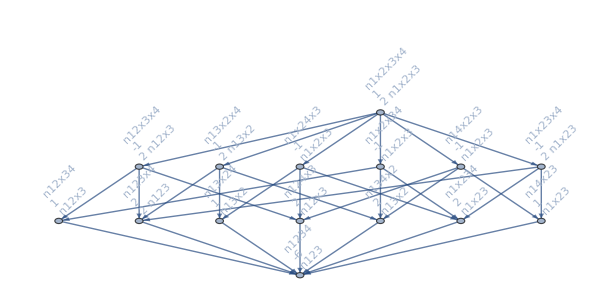

```mathematica
MobiusGraph4[K4Key,allGraphs4]
```

```mathematica
Table[
{Length[ListofVars[allGraphs4[k,"colofour"]]],allGraphs4[k,"colofourrealnull"],allGraphs4[k,"colofour"]}
,{k,allGraphs4NullAtomKeys}
]//Sort//TableForm
```

1 | n1234 | v1234
2 | n123x4 | v1234+v123x4
2 | n124x3 | v1234+v124x3
2 | n12x34 | v1234+v12x34
2 | n134x2 | v1234+v134x2
2 | n13x24 | v1234+v13x24
2 | n14x23 | v1234+v14x23
2 | n1x234 | v1234+v1x234
5 | n12x3x4 | v1234+v123x4+v124x3+v12x34+v12x3x4
5 | n13x2x4 | v1234+v123x4+v134x2+v13x24+v13x2x4
5 | n14x2x3 | v1234+v124x3+v134x2+v14x23+v14x2x3
5 | n1x23x4 | v1234+v123x4+v14x23+v1x234+v1x23x4
5 | n1x24x3 | v1234+v124x3+v13x24+v1x234+v1x24x3
5 | n1x2x34 | v1234+v12x34+v134x2+v1x234+v1x2x34
15 | n1x2x3x4 | v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4